```mathematica
primePoints[n_Integer,allSteps_:True]:=ReIm@Accumulate@
If[TrueQ@allSteps (* don't jump. just walk *),
Join[{0,1},ⅈ^-PrimePi@Range[n-1]],
Join[{0,0},Prime[Range@PrimePi@n],{n}]//
MapIndexed[-# ⅈ^-#2[[1]]&,Differences@#]&]
```

```mathematica
primeTurn[n_Integer,dot_:False]:=Module[{p,q,r,s,points},
points=primePoints[n,n<10^6 && dot || n<400];
s=If[dot,AbsolutePointSize,AbsoluteThickness]@Which[
n>10^6,Tiny,n>50000,Small,n>2500,Medium,True,Large];
r=points~CoordinateBounds~If[n>1000,6~Log~n,1];
p={s,Red,If[dot,Point@{0,0},points[[-2;;]]//Line]};
Graphics[{s,Blue,If[dot,Point,Line]@points}~Join~p,
PlotRange->r,ImageSize->Part[Differences/@r,1,1]35]]
```

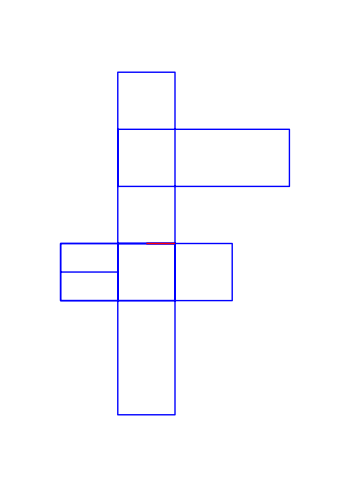

```mathematica
primeTurn[80]
```

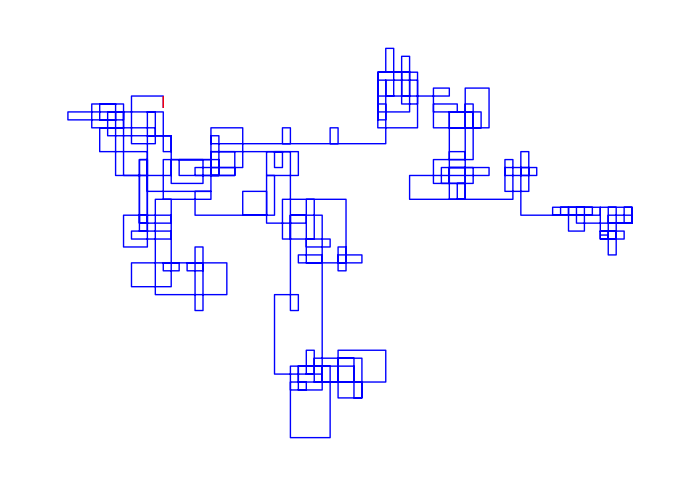

```mathematica
Show[primeTurn[2470],ImageSize->700]
```

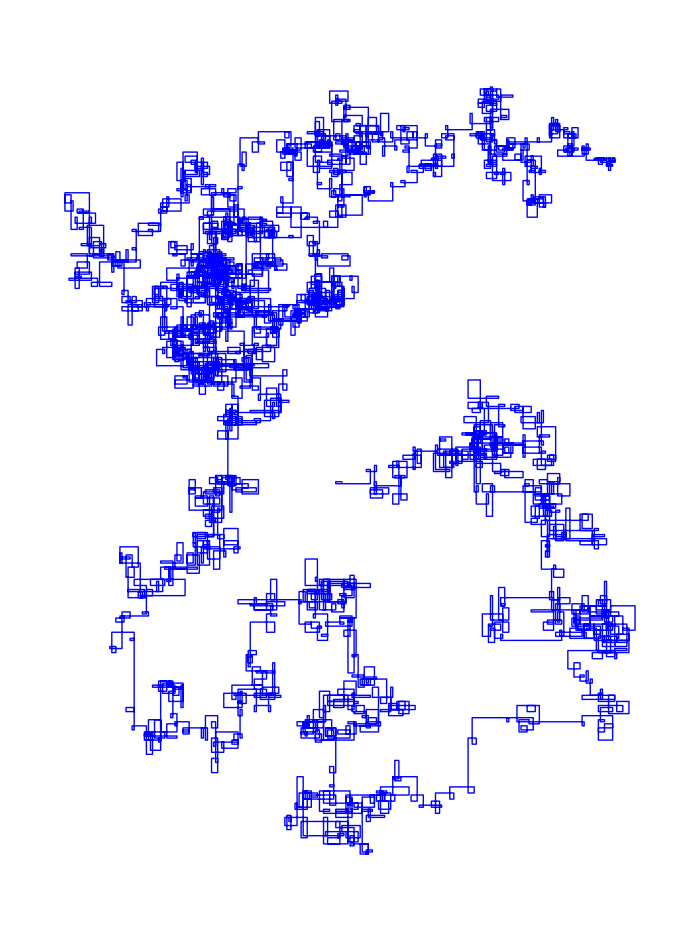

```mathematica
Show[primeTurn[50000],ImageSize->700]
```

```mathematica
Export["usa.png",Show[{primeTurn[10^6+40000],Graphics@{PointSize@Medium,Red,Point@{0,0}}},ImageSize->1200]];
```

```mathematica
With[{n=5},Export[ToString@n<>"mil.png",Show[{primeTurn[10^6n,n>5],
Graphics[{PointSize@Medium,Red,Point@{0,0}}]},ImageSize->2000]]];
```

```mathematica
makeGif=Module[{images,p,q,r=Cases[{##},_Integer],s,points},
images=Array[Image@Array[1&,{750,1000}]&,1+Max@r-Min@r];
Do[points=primePoints[n-1+Min@r,n<400];
s=CoordinateBounds[points,1];
q=Flatten[Differences/@s];
If[Last@Ratios[q]>3/4,
s[[1]]+={-q,q}.{-3,4}/6,s[[2]]-={-q,q}.{-3,4}/8];
p={AbsoluteThickness@Large,Blue,Line[points]};
q=Max[Differences/@s];
images[[n]]=Graphics[p~Join~{Red,Line@points[[-2;;]]},
PlotRange->s,ImageSize->30q]~Magnify~(100/q/3),
{n,Length@images}];
Last@Cases[{"walk.gif",##},_String]~Export~images]&;
```

```mathematica
makeGif["walk.gif",3,387];
```

```mathematica
showOff[n_Integer]:=Module[{p,q,r},
p=Accumulate@ReIm@Prepend[ⅈ^-PrimePi@Range[n-1],0];
r=CoordinateBounds[p,1];
q=AbsoluteThickness@Which[n>10^6,Tiny,n>50000,Small,n>2500,Medium,True,Large];
Graphics[{q,Blue,Line@p,Red,Line@p[[;;2]],Green,Line@p[[-2;;]]},
PlotRange->r,ImageSize->Part[Differences/@r,1,1]35]]
```